# Nekaj nalog z zaporedji in limitami

### Naloge:

#### 1. Naloga:

Najprej definiramo naše zaporedje z imenom zaporedje1.

```mathematica
zaporedje1[n_] := 1000^n / n!
```

Z funkcijo Map, ki uporabi funkcijo na vseh elementih seznama, bomo pogledali prvih 5 členov našega zaporedja.

```mathematica
Map[zaporedje1,Range[5]]
```

{1000,500000,500000000/3,125000000000/3,25000000000000/3}

Kot vse kaže, to zaporedje na začetku narašča, zato si poglejmo nekaj več členov in z funkcijo N poglejmo približke.

```mathematica
N[Map[zaporedje1, Range[12]]]
```

{1000.,500000.,1.66667×10^8,4.16667×10^10,8.33333×10^12,1.38889×10^15,1.98413×10^17,2.48016×10^19,2.75573×10^21,2.75573×10^23,2.50521×10^25,2.08768×10^27}

Naše zaporedje je sestavljeno iz geometrijskega zaporedja in fakultete. Ker vemo, da fakulteta narašča hitreje od poljubnega geometrijskega zaporedja, lahko pričakujemo, da bo naša limita 0. (Fakulteta narašča hitreje od nekod dalje. Če je osnova (v našem primeru 1000) zelo velika, bo na začetku nekaj časa geometrijsko zaporedje večje od fakultete.)

Najdimo največje število v našem zaporedju. Najprej si poglejmo nekaj naključnih členov zaporedja, da bomo vedeli kje približno se nahaja.

```mathematica
N[Map[zaporedje1, {40, 150, 400,750,1200,1400}]]
```

{1.22562×10^72,1.75028×10^187,1.56165761146563×10^331,3.87476227580573×10^417,1.57460748011616×10^424,2.88964779621184×10^401}

Od tod sklepamo, da se največja vrednost nahaja na intervalu [750, 1400].

```mathematica
N[Max[Map[zaporedje1, Range[750, 1400]]]]
```

2.48516814326678×10^432

Z funkcijo Ordering si poglejmo na katerem mestu je ta člen.

```mathematica
Ordering[Map[zaporedje1, Range[1400]], -1]
```

{1000}

n = 1000 je tudi logična rešitev, saj od 1000 naprej naš člen “množimo” z  1000/m;   m > 1000   ->  1000/m  <  1.

Narišimo še graf in se s funkcijo Limit še prepričajmo, da je naša limita res enaka 0.

```mathematica
Plot[zaporedje1[n],{n, 0,2150}]
```

-Graphics-

```mathematica
Limit[1000^n / n!, n-> Infinity]
```

0

Limita zaporedja zaporedje1 je enaka 0.

Z funkcijo Manipulate, bi radi še prikazali, kako se zaporedje a^n/(n!)obnaša v odvisnosti od osnove a.

```mathematica
Manipulate[Plot[a^n/n!,{n,0,80},PlotRange->All],{a,1,50}]
```

Iz grafa lahko razberemo, da maksimum zaporedja močno narašča, ko povečujemo a. Poleg tega pa se maksimum tudi premika v desno, in je na mestu n = a.

#### 2. Naloga:

Določi limito rekurzivno podanega zaporedja z začetnim členom a_0 = 0.5 in predpisom:

Najprej definiramo naše zaporedje in začetni člen z imenom zaporedje2.

```mathematica
zaporedje2[n_]:=(n+1)^2 /(1.1*n^2) * zaporedje2[n-1]
zaporedje2[0] = 0.5;
```

Enako kot prej, bomo z funkcijo Map pogledali prvih nekaj členov zaporedja.

```mathematica
Map[zaporedje2,Range[8]]
```

{1.81818,3.71901,6.01052,8.53767,11.1766,13.8296,16.4211,18.8935}

Namesto da bi uporabili funkciji Map in Range na večjem intervalu kot pri prejšnji nalogi, najprej narišimo graf. Mogoče bomo s pomočjo grafa lahko več kaj sklepali.

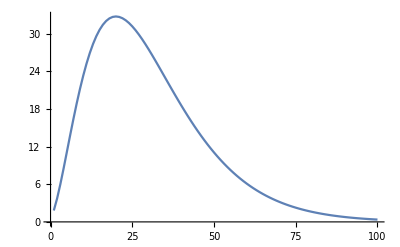

```mathematica
ListLinePlot[{Map[zaporedje2, Range[100]]}]
```

Opazimo, da zaporedje narašča nekje do 20. člena, nato pa začne padati in se približuje 0. Poglejmo si največjo vrednost našega zaporedja in izračunajmo limito.

```mathematica
Map[zaporedje2,Range[15,25]]
Max[Map[zaporedje2,Range[15,25]]]
Ordering[Map[zaporedje2, Range[15,25]], -1] + 14 (*prištejemo 14, ker smo začeli gledati na 15. mestu*)
```

{30.6422,31.4474,32.0508,32.4645,32.7016,32.7759,32.7016,32.4928,32.1633,31.7267,31.196}

32.7759

{20}

Za lažje računanje limite, lahko naše rekurzivno zaporedje zapišemo z splošno formulo:

```mathematica
Limit[n^2 / 1.1^n, n -> Infinity]
```

0.

Pokazali smo, da je limita našega zaporedja zaporedje2 enaka 0.

#### 3. Naloga:

Poišči limito zaporedja v kompleksni ravnini.

Najprej definiramo naše zaporedje z imenom zaporedje3.

```mathematica
zaporedje3[n_] := (2 + 5n*I) / (n(1 + I))
```

Narišimo naše zaporedje v kompleksni ravnini.

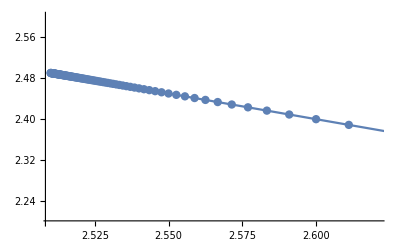

```mathematica
ListLinePlot[Map[Function[Tooltip[{Re[#1],Im[#1]}]],Map[zaporedje3,Range[100]]],PlotRange->{2.2,2.6},Mesh -> All]
```

Iz grafa lahko razberemo, da se zanše zaporedje približuje točki 2/5 + 2/5 i.
Pomagamo si lahko z dejstvom, da zaporedje kompleksnih števil konvergira natanko tedaj, ko konvergirata zaporedji realnih in imaginarnih komponent. Naše zaporedje lahko zapišemo kot:

Sedaj definirajmo zaporedji realno in imaginarno.

```mathematica
realno[n_] := (2 + 5n) / (2n)
imaginarno[n_] := (5n - 2) / (2n)
```

Poglejmo si limiti teh dveh podzaporedij.

```mathematica
Limit[realno[n], n -> Infinity]
Limit[imaginarno[n], n -> Infinity]
```

5/2

5/2

Iz grafa smo razbrali pravilno. Poglejmo si se skupno limito našega zaporedja zaporedje3.

```mathematica
Limit[zaporedje3[n], n -> Infinity]
```

5/2+(5 ⅈ)/2

Pokazali smo, da se naše zaporedje res približuje točki 2/5 + 2/5 i.